## Definiciones

```mathematica
SetDirectory[NotebookDirectory[]];Get["../../../QuantumWalks.wl"]
```

Coin::shdw: Symbol Coin appears in multiple contexts {QuantumWalks`,Global`}; definitions in context QuantumWalks` may shadow or be shadowed by other definitions.

Shift::shdw: Symbol Shift appears in multiple contexts {QuantumWalks`,Global`}; definitions in context QuantumWalks` may shadow or be shadowed by other definitions.

```mathematica
(*moneda*)
ClearAll[c]
c[θ_,α_,ϕ_]:=FullSimplify[MatrixExp[-I*θ/2.*({Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}.(PauliMatrix/@{1,2,3}))]]
```

```mathematica
(*shift*)
ClearAll[S]
S[t_]:=KroneckerProduct[DiagonalMatrix[ConstantArray[1,2t],1],{{0,0},{0,1.}}]+KroneckerProduct[DiagonalMatrix[ConstantArray[1,2t],-1],{{1.,0},{0,0}}]
```

```mathematica
S[1].{0,0,1,0,0,0}
```

{0.,0.,0.,0.,1.,0.}

```mathematica
(*paso DTQW*)
ClearAll[U]
U[t_,θ_,α_,ϕ_]:=S[t].KroneckerProduct[IdentityMatrix[2t+1],c[θ,α,ϕ]]
```

```mathematica
U[1,θ,α,ϕ]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.+1. ⅇ^((0.-0.5 ⅈ) θ) | 0. | 0.
0.+1. ⅇ^((0.+0.5 ⅈ) θ) | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.+1. ⅇ^((0.-0.5 ⅈ) θ)
0. | 0. | 0.+1. ⅇ^((0.+0.5 ⅈ) θ) | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
U[2,θ,α,ϕ].ArrayPad[U[1,θ,α,ϕ].{0,0,1,0,0,0},2]/.{θ->0.52Pi,α->0.23Pi,ϕ->1.75Pi}
```

{0.,0.,0.,0.,0.,0.,0.,0.,-0.0627905+0.998027 ⅈ,0.}

```mathematica
(*DTQWAnalytical*)
ClearAll[DTQWAnalytical]
DTQWAnalytical[t_,θ_,α_,ϕ_]:=Fold[ArrayPad[U[#2,θ,α,ϕ].#1,2]&,{0,0,0,1,0,0},Range[t]]
DTQWAnalyticalAnalytical[psi0_,t_,theta_,alpha_,phi_]:=Module[{validInput},validInput=MatchQ[psi0,{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}];
If[!validInput,Message[DTQWAnalyticalAnalytical::invalidpsi0,psi0];
Return[$Failed];];
Fold[ArrayPad[U[#2,theta,alpha,phi].#1,2]&,psi0,Range[t]]]

DTQWAnalyticalAnalytical::invalidpsi0="ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: `1`.";
```

```mathematica
(*probabilidades espacio*)
ProbDistPosition[ψ_]:=Total/@(Abs[Partition[ψ,2]]^2)
```

```mathematica
ProbDistPosition[DTQWAnalyticalAnalytical[{0,0,1,0,0,0},3,θ,α,ϕ]]/.{θ->0.52Pi,α->0.23Pi,ϕ->1.75Pi}
```

{0,0.,0.,0.,0.,0.,0.,1.,0}

```mathematica
(*expected position*)
ClearAll[ExpPosition]
ExpPosition[t_,θ_,α_,ϕ_]:=ProbDistPosition[DTQWAnalyticalAnalytical[t,θ,α,ϕ]].Range[-t-1,t+1]
ExpPosition[ψ_]:=Module[{t=(Length[ψ]/2-3)/2},Chop[ProbDistPosition[ψ].Range[-t-1,t+1]]]
```

```mathematica
MyManipulate[t_]:=
Manipulate[
Plot[ExpPosition[t],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->30],
ImageSize->600,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->25],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

## Gráficas de contra θ

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,0,1.,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->1000,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
(* Export["/home/jadeleon/Documents/quantum_walks/ja/video.mp4",frames,"ImageSize"->480,"FrameRate"->16] *)
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1.,0,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->1000,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |0⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,1./√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |+_x⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,-1./√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |-_x⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,ⅈ/√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |+_y⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,-ⅈ/√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |-_y⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,-0.38268343236508984,0.9238795325112867,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |H_-⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,0.9238795325112867,0.3826834323650898,0,0},#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |H_+⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
RandomQubitState[seed_Integer]:=Module[{θ,ϕ},
BlockRandom[
SeedRandom[seed];
θ=RandomReal[{0,π}];
ϕ=RandomReal[{0,2 π}];
{θ,ϕ,0,0,Cos[θ/2],Exp[ⅈ ϕ] Sin[θ/2],0,0}
]
]
```

```mathematica
RandomQubitState[67]
```

{0.129855,1.83464,0,0,0.997893,-0.0169209+0.0626364 ⅈ,0,0}

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[RandomQubitState[67][[3;;]],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = random, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
RandomQubitState[865]
```

{1.67187,3.73153,0,0,0.670483,-0.61652-0.412742 ⅈ,0,0}

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[RandomQubitState[865][[3;;]],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = random, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
RandomQubitState[93]
```

{1.84151,1.85851,0,0,0.60522,-0.225889+0.763336 ⅈ,0,0}

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[RandomQubitState[93][[3;;]],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = random, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
Table[n π/4.,{n,0,8}]
```

{0.,0.785398,1.5708,2.35619,3.14159,3.92699,4.71239,5.49779,6.28319}

```mathematica
coin1={θcoin,ϕcoin,0,0,Cos[θcoin/2],Exp[ⅈ ϕcoin] Sin[θcoin/2],0,0}/.{θcoin->0.2,ϕcoin->0}
```

{0.2,0,0,0,0.995004,0.0998334,0,0}

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[coin1[[3;;]],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = random, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
PlotLegends->Range[5],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
ExpValPosition[ψ_,t_]:=ProbDistPosition[ψ].Range[-t-1,t+1]
```

```mathematica
A=ProbDistPosition[DTQWAnalyticalAnalytical[{0,0,1,0,0,0},3,0.52π,0.23π,1.75π]]
```

{0,0.136932,0.,0.108026,0.,0.302759,0.,0.452283,0}

```mathematica
ExpValPosition[DTQWAnalyticalAnalytical[{0,0,1,0,0,0},3,0.52π,0.23π,1.75π],3]
```

1.14079

```mathematica
ψ0={0,0,1/√2.,1/√2.,0,0};tmax=5;
Prepend[Table[{t,ExpValPosition[DTQWAnalyticalAnalytical[ψ0,t,0.52π,0.23π,1.75π],t]},{t,tmax}],{0,0}]
```

{{0,0},{1,0.839486},{2,1.28878},{3,1.42484},{4,1.47656},{5,1.65814}}

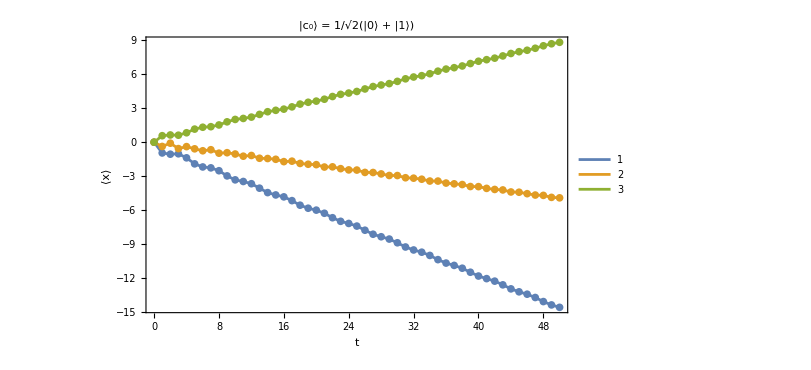

```mathematica
ψ0={0,0,1/√2.,1/√2.,0,0};tmax=50;
ListPlot[{
Prepend[Table[{t,ExpValPosition[DTQWAnalyticalAnalytical[ψ0,t,3Pi/2.,0.39Pi,1.3Pi],t]},{t,tmax}],{0,0}],
Prepend[Table[{t,ExpValPosition[DTQWAnalyticalAnalytical[ψ0,t,Pi,0.39Pi,1.3Pi],t]},{t,tmax}],{0,0}],
Prepend[Table[{t,ExpValPosition[DTQWAnalyticalAnalytical[ψ0,t,Pi+3Pi/2,0.39Pi,1.3Pi],t]},{t,tmax}],{0,0}]},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm@HoldForm[t], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLegends->Automatic,
PlotLabel->Style["|c_0⟩ = 1/√2(|0⟩ + |1⟩)",Black,FontSize->28]
]
```

## Gráficas de contra α

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,1./√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{α,0,Pi},
PlotRange->{All,{-(t+0.05 t),t+0.05 t}},
Frame->True,
FrameLabel->{HoldForm[α],"⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |+_x⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,4}],Automatic}},Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
],
{θ,0,2 Pi},{ϕ,0,2 Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,-1./√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{α,0,Pi},
PlotRange->{All,{-(t+0.05 t),t+0.05 t}},
Frame->True,
FrameLabel->{HoldForm[α],"⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |-_x⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,4}],Automatic}},Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
],
{θ,0,2 Pi},{ϕ,0,2 Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,ⅈ/√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{α,0,Pi},
PlotRange->{All,{-(t+0.05 t),t+0.05 t}},
Frame->True,
FrameLabel->{HoldForm[α],"⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |+_y⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,4}],Automatic}},Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
],
{θ,0,2 Pi},{ϕ,0,2 Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,-ⅈ/√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{α,0,Pi},
PlotRange->{All,{-(t+0.05 t),t+0.05 t}},
Frame->True,
FrameLabel->{HoldForm[α],"⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |-_y⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,4}],Automatic}},Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
],
{θ,0,2 Pi},{ϕ,0,2 Pi}]
```

## Gráficas de contra α

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,1./√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{ϕ,0,2 Pi},PlotRange->{All,{-(t+0.05 t),t+0.05 t}},Frame->True,FrameLabel->{HoldForm[ϕ],"⟨x⟩"},FrameStyle->Directive[Black,FontSize->28],ImageSize->1000,PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |+_x⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
],{θ,0,2 Pi},{α,0,Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,-1./√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{ϕ,0,2 Pi},PlotRange->{All,{-(t+0.05 t),t+0.05 t}},Frame->True,FrameLabel->{HoldForm[ϕ],"⟨x⟩"},FrameStyle->Directive[Black,FontSize->28],ImageSize->1000,PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |-_x⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
],{θ,0,2 Pi},{α,0,Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,ⅈ/√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{α,0,Pi},
PlotRange->{All,{-(t+0.05 t),t+0.05 t}},
Frame->True,
FrameLabel->{HoldForm[α],"⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |+_y⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,4}],Automatic}},Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
],
{θ,0,2 Pi},{ϕ,0,2 Pi}]
```

```mathematica
t=5;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalyticalAnalytical[{0,0,1./√2.,-ⅈ/√2.,0,0},#,θ,α,ϕ]]&/@Range[5]],{α,0,Pi},
PlotRange->{All,{-(t+0.05 t),t+0.05 t}},
Frame->True,
FrameLabel->{HoldForm[α],"⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = |-_y⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,4}],Automatic}},Epilog->{Black,InfiniteLine[{{0,0},{100,0}}]}
],
{θ,0,2 Pi},{ϕ,0,2 Pi}]
```

```mathematica
c[Pi,0.39Pi,1.3Pi].c[3Pi/2.,0.39Pi,1.3Pi]//Chop//MatrixForm
```

(-0.707107+0.239524 ⅈ | -0.538242-0.391055 ⅈ
0.538242-0.391055 ⅈ | -0.707107-0.239524 ⅈ)

```mathematica
-c[Pi/2.,0.39Pi,1.3Pi]//Chop//MatrixForm
```

(-0.707107+0.239524 ⅈ | -0.538242-0.391055 ⅈ
0.538242-0.391055 ⅈ | -0.707107-0.239524 ⅈ)

```mathematica
c[θ,α,ϕ]//Chop//MatrixForm
```

(ⅇ^((0.+0.5 ⅈ) θ) | 0
0 | ⅇ^((0.-0.5 ⅈ) θ))

```mathematica
c[Pi,0.39Pi,1.3Pi].c[3Pi/2.,0.39Pi,1.3Pi]//Chop//MatrixForm
```

(-0.707107+0.239524 ⅈ | -0.538242-0.391055 ⅈ
0.538242-0.391055 ⅈ | -0.707107-0.239524 ⅈ)

```mathematica
-c[Pi/2.,0.39Pi,1.3Pi]//Chop//MatrixForm
```

(-0.707107+0.239524 ⅈ | -0.538242-0.391055 ⅈ
0.538242-0.391055 ⅈ | -0.707107-0.239524 ⅈ)

```mathematica
c[θ,α,ϕ]//Chop//MatrixForm
```

(ⅇ^((0.+0.5 ⅈ) θ) | 0
0 | ⅇ^((0.-0.5 ⅈ) θ))